```mathematica
x={-1.0000,0.7778,2.5556,4.3333,6.1111,7.8889,9.6667,11.4444,13.2222,15.0000};
gn={0.9703,-0.6151,-0.2638,0.7263,0.1395,-0.3525,0.2280,0.3730,-0.0837,-0.0281};
evn={0.4971,0.7369,-0.3897,0.1934,1.1458,0.7730,0.5974,1.2826,1.5335,1.3305};
```

```mathematica
h[i_,y_]:=Product[(y-x[[j]])^2/(x[[i]]-x[[j]])^2,{j,DeleteCases[Range[1,Length[x]],i]}]
```

```mathematica
dh[i_,y_]:=h[i,y]*Sum[1/(x[[i]]-x[[j]]),{j,DeleteCases[Range[1,Length[x]],i]}]
```

```mathematica
ZZ[y_]:=Sum[(evn[[j]]+(gn[[j]]-2*evn[[j]]*dh[j,y])*(y-x[[j]]))*h[j,y]^2,{j,Range[1,Length[x]]}]
```

```mathematica
u=14.7588;
```

```mathematica
For[j=1,j<=Length[x],j++,Print[h[j,u]]]
```

0.000105454

0.0108528

0.227949

1.70025

5.55979

8.80966

7.12709

3.09011

0.898455

0.450149

```mathematica
For[j=1,j<=Length[x],j++,Print[dh[j,u]]]
```

-0.000167808

-0.0104871

-0.140137

-0.5897

-0.625432

0.991016

2.4719

1.89972

0.868178

0.716316

```mathematica
ZZ[u]
```

-1266.52

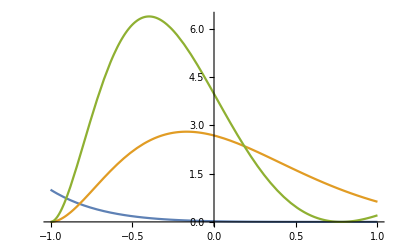

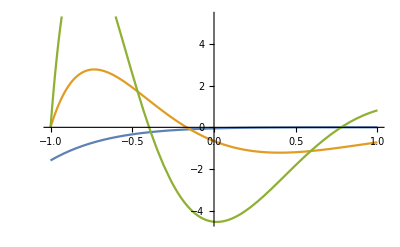

```mathematica
Plot[{h[1,z],h[2,z],h[3,z]},{z,-1,1}]
Plot[{dh[1,z],dh[2,z],dh[3,z]},{z,-1,1}]
```

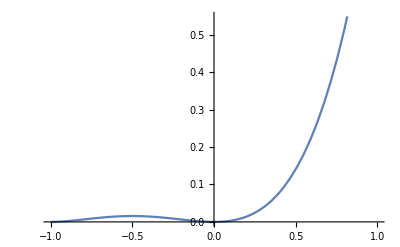

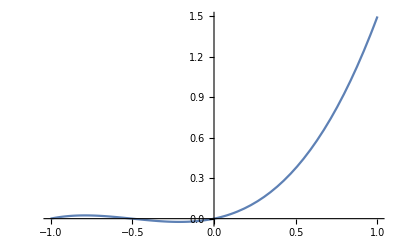

```mathematica
Plot[{h[3,z]},{z,-1,1}]
Plot[{dh[3,z]},{z,-1,1}]
```

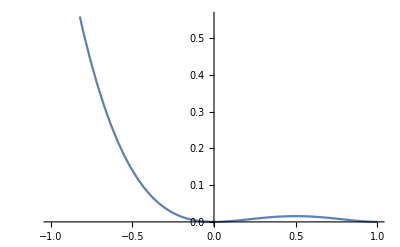

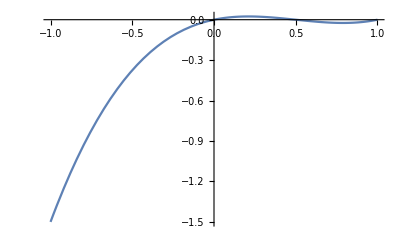

```mathematica
Plot[{h[2,z]},{z,-1,1}]
Plot[{dh[2,z]},{z,-1,1}]
```

```mathematica
Expand[(1-d)^4]
```

1-4 d+6 d^2-4 d^3+d^4